```mathematica
SetDirectory[NotebookDirectory[]];
```

First figure out how many samples we managed to align “completely.” fastq-dump can return success when a download has actually failed, and in this case, we have found empirically that the error persists when reattempting downloads. Moreover, some unusual samples may have been incorrectly processed by Rail-RNA. The Sequence Read Archve records the number of spots per sample, which is either half the number of mates (for paired-end samples) or the number of reads (for single-end samples). We compare this value with the number of reads counted by Rail-RNA for a given sample to assess whether an entire sample was aligned using incomplete.py in this repo. incomplete.py also records whether a sample is likely incorrectly annotated as paired- or single-end: that is, if a sample is single-end but has exactly half as many spots reported by SRA as reads counted by Rail, then the sample is likely paired-end; and if the sample is paired-end but Rail counts more reads than there are spots, then the sample is likely single-end.

(7 samples in incomplete.tsv had spot counts = 0 on SRA, yet we could download their reads. We assume they were downloaded successfully.)

Run

join -1 1 -2 1 -a 1 <(cat incomplete.tsv | tail -n +2 | grep -v NA | cut -f1 | less | sort | uniq -c | sed ‘s/^ *//g’ | awk ‘{print $2 “\t” $1}’) <(cut -f2 intropolis.idmap.v2.hg38.tsv | sort | uniq -c | sed ‘s/^ *//g’ | awk ‘{print $2 “\t” $1}’) | awk ‘{print $1 “\t” $2 “\t” $3 “\t” $2/$3}’ | sort -k2,2nr >incomplete_projects.tsv

on the output of incomplete.py. This counts the number of incompletely downloaded samples for projects with at least one incompletely downloaded sample.

Load files characterizing incompletely downloaded samples.

```mathematica
incompleteDownloads = Import["!grep -v NA incomplete.tsv", "TSV"];
```

```mathematica
largerLabelForm [x_,y___]:= Text[Style[x, FontFamily->"Arial", FontSize->Scaled[.053],Bold,TextAlignment->Left], y]
```

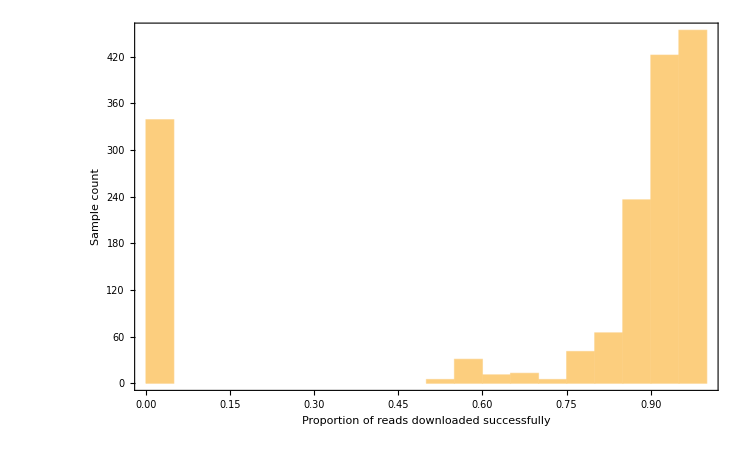

```mathematica
padding2={{75,10},{60,12}};incompleteHistogram=Show[Histogram[incompleteDownloads[[All,7]]//N, 15,Frame->True,ImageSize->baseImageSize,ImagePadding->padding2,BaseStyle->{FontFamily->"Arial",FontSize->15},FrameLabel->{Style["Proportion of reads downloaded successfully", 22], Style["Sample count", 22]}]]
```

```mathematica
Export["incomplete.pdf", incompleteHistogram]
```

incomplete.pdf

Get projects contributing the most incompletely downloaded samples, the number of incompletely downloaded samples per project, the mean proportion of reads downloaded per project, and associated standard deviations by running

 paste <(head -n 15 incomplete_projects.tsv | cut -f1,2) <(for i in $(head -n 15 incomplete_projects.tsv | cut -f1); do grep -w $i <(grep -v NA incomplete.tsv) | cut -f7 | awk ‘{for(i=1;i<=NF;i++) {sum[i] += $i; sumsq[i] += ($i)^2}} END {for (i=1;i<=NF;i++) { print sum[i]/NR “\t” sqrt((sumsq[i]-sum[i]^2/NR)/NR)} }’; done) >top_incomplete_projects.tsv
 
 It turns out that every samples for which fewer than 50% of its reads were downloaded by Rail actually had _0_ downloaded reads. So we define a sample as “aligned” if our computation above gives that >= 50% of its reads were downloaded. This excludes 339 samples listed in intropolis.idmap.v2.hg38.tsv, and they are recorded in noreads.txt. (Note that we may actually be overestimating the number of incompletely downloaded samples because the number of spots in a given sample may have been misreported.)
 
  Check top_incomplete_projects.tsv for results. Note that incomplete.sh reproduces incomplete.tsv, incomplete_projects.tsv, and top_incomplete_projects.tsv, so commands above need not be copy-pasted.
  
To obtain the number of samples we aligned, subtract 339 from the number of lines in intropolis.idmap.v2.hg38.tsv to obtain

```mathematica
samplesAligned=50099 - 339
```

49760

Now study number of junctions supported by ≥ K samples.

```mathematica
aggregatedJunctionCounts=Drop[Import["hg38.sample.stats.tsv", "TSV"], 1];
```

```mathematica
totalJunctions = Transpose[Transpose[aggregatedJunctionCounts][[{1,2}]]];annotatedJunctions=Transpose[Transpose[aggregatedJunctionCounts][[{1,3}]]];exonSkipJunctions=Transpose[Transpose[aggregatedJunctionCounts][[{1,4}]]];altStartEndJunctions=Transpose[Transpose[aggregatedJunctionCounts][[{1,5}]]];
novelJunctions=exonSkips=Transpose[Transpose[aggregatedJunctionCounts][[{1,6}]]];
```

```mathematica
Length[annotatedJunctions]
```

41948

Proportion of junctions in ≥ 20k samples that are annotated

```mathematica
annotatedJunctions[[41948-19999]]
```

{20000,104565}

```mathematica
annotatedJunctions[[41948-19999]][[2]]/totalJunctions[[41948-19999]][[2]]//N
```

0.997939

```mathematica
exonSkipAnnotatedJunctions = Transpose[{annotatedJunctions[[All,1]],annotatedJunctions[[All,2]]+exonSkipJunctions[[All,2]]}];
someEvidenceJunctions = Transpose[{annotatedJunctions[[All,1]],annotatedJunctions[[All,2]]+exonSkipJunctions[[All,2]]+altStartEndJunctions[[All,2]]}];
```

```mathematica
mathematicaColors=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

Introduce levels of evidence, and annotated with junction counts for ≥ 1000 samples

```mathematica
labelForm [x_,y___]:= Text[Style[x, FontFamily->"Arial", FontSize->Scaled[.033],Bold,TextAlignment->Left], y]
```

```mathematica
idx=41948-2499
```

39449

```mathematica
bigLabelForm [x_,y___]:= Text[Style[x, FontFamily->"Arial", FontSize->Scaled[.055],Bold,TextAlignment->Right], y]
```

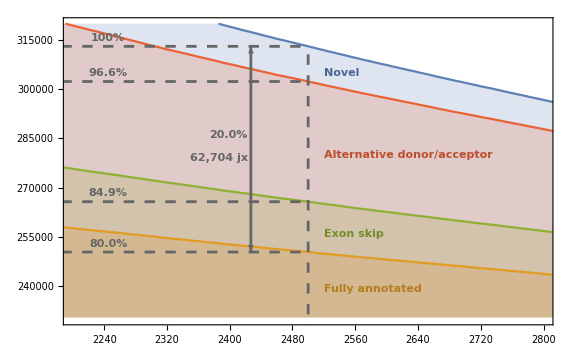

```mathematica
dashedColor=Darker[Gray,0.2];numberStartPos=2245;adjust=2600;insetAnnotationPlot=Show[ListPlot[{totalJunctions,annotatedJunctions,exonSkipAnnotatedJunctions, someEvidenceJunctions}, Joined->True, PlotRange->{{2200, 2800},{230000,320000}}, Filling->Axis,  Frame->True,ImageSize->Large, BaseStyle->{FontFamily->"Arial",FontSize->15}], Graphics[{Directive[Thickness[0.0035],Dashing[0.013], dashedColor],Line[{{2500,0},totalJunctions[[idx]]}],Line[{{0,totalJunctions[[idx]][[2]]},totalJunctions[[idx]]}],Line[{{0,annotatedJunctions[[idx]][[2]]},annotatedJunctions[[idx]]}],
Line[{{0,exonSkipAnnotatedJunctions[[idx]][[2]]},exonSkipAnnotatedJunctions[[idx]]}],Line[{{0,someEvidenceJunctions[[idx]][[2]]},someEvidenceJunctions[[idx]]}],Directive[{Dashing[None],Arrowheads[{-.05,.05}]}], Arrow[{{2427,annotatedJunctions[[idx]][[2]]},{2427,totalJunctions[[idx]][[2]]}}],bigLabelForm[ToString[NumberForm[N[100-annotatedJunctions[[idx,2]]/totalJunctions[[idx,2]]*100,3],DigitBlock->3]]<>"%",{2423, 286000}, {1,0}],labelForm[ToString[NumberForm[totalJunctions[[idx,2]]-annotatedJunctions[[idx,2]],DigitBlock->3]]<>" jx", {2423, 279000},{1,0}],labelForm["100%",{numberStartPos,totalJunctions[[idx]][[2]]+adjust}],labelForm[ToString[NumberForm[N[someEvidenceJunctions[[idx,2]]/totalJunctions[[idx,2]]*100,3],DigitBlock->3]]<>"%", {numberStartPos,someEvidenceJunctions[[idx]][[2]]+adjust}],
labelForm[ToString[NumberForm[N[annotatedJunctions[[idx,2]]/totalJunctions[[idx,2]]*100,3],DigitBlock->3]]<>"%", {numberStartPos,annotatedJunctions[[idx]][[2]]+adjust}],
labelForm[ToString[NumberForm[N[exonSkipAnnotatedJunctions[[idx,2]]/totalJunctions[[idx,2]]*100,3],DigitBlock->3]]<>"%", {numberStartPos,exonSkipAnnotatedJunctions[[idx]][[2]]+adjust}],(*Directive[Thickness[0.0035],Arrowheads[.035],Dashing[None], dashedColor],Arrow[{{1000,totalJunctions[[idx]][[2]]+41000},{1000,totalJunctions[[idx]][[2]]+100}}],labelForm[ToString[NumberForm[N[100-annotatedJunctions[[idx,2]]/totalJunctions[[idx,2]]*100],3]]<>"% of jx unannotated, but\n"<>ToString[NumberForm[someEvidenceJunctions[[idx,2]]/totalJunctions[[idx,2]]*100//N,3]]<>"% of jx have donor and/or\nacceptor site in annotation", {1005, 330000}, {-1,0}],*)Darker[mathematicaColors[[1]], 0.2],labelForm["Novel",{2520,305000}, {-1,0}],Darker[mathematicaColors[[4]], 0.2],labelForm["Alternative donor/acceptor",{2520,280000}, {-1,0}],Darker[mathematicaColors[[3]], 0.2],labelForm["Exon skip",{2520,256000}, {-1,0}],Darker[mathematicaColors[[2]], 0.2],labelForm["Fully annotated",{2520,239000}, {-1,0}]}]]
```

```mathematica
baseImageSize={576,408}*1.3
```

{748.8,530.4}

```mathematica
bigAnnotationPlot=ListPlot[{totalJunctions,annotatedJunctions,exonSkipAnnotatedJunctions, someEvidenceJunctions}, Joined->True, PlotRange->{{0, 40000},{0,700000}}, Filling->Axis,  Frame->True,ImageSize->baseImageSize, BaseStyle->{FontFamily->"Arial",FontSize->15},Epilog->Inset[insetAnnotationPlot, {24000,420000}, Automatic, 31000],FrameLabel->{Style["Minimum number S of samples in which jx is called", 22], Style["Junction (jx) count J", 22]}]
```

-Graphics-

```mathematica
magnifyingGlass=Import["mag.png"]
```

-Graphics-

```mathematica
fig1a=Show[bigAnnotationPlot,Graphics[{EdgeForm[Directive[Gray, Thickness[.0015]]],Transparent,Rectangle[{2200, 230000},{2800,320000}]}],Graphics[{Gray,Arrow[{{3300,320000},{8000,410000}}]}],  Graphics[{Opacity[0.5],Inset[magnifyingGlass,{4000,350000},{0,0},2000]}], Graphics[{Black, Text[Style["a", FontFamily->"Arial", FontSize->40], {2500, 640000}]}],ImageSize->baseImageSize]
```

-Graphics-

```mathematica
statsBySample=Drop[Import["!awk '$6>=100000' "<>NotebookDirectory[]<>"hg38.stats_by_sample.tsv", "TSV"], 1];
```

```mathematica
jxConsidered=Length[statsBySample]
```

25207

Overlaps by sample-->

```mathematica
largerLabelForm [x_,y___]:= Text[Style[x, FontFamily->"Arial", FontSize->Scaled[.053],Bold,TextAlignment->Left], y]
```

```mathematica
jxHistList=HistogramList[statsBySample[[All,11]]/statsBySample[[All,10]], 15]
```

{{0,1/20,1/10,3/20,1/5,1/4,3/10,7/20,2/5,9/20,1/2,11/20,3/5,13/20,7/10,3/4,4/5,17/20,9/10,19/20,1},{7,1,0,0,1,3,12,3,3,2,6,4,12,3,6,6,22,77,311,24728}}

```mathematica
lastBin=jxHistList[[2,20]]
```

24728

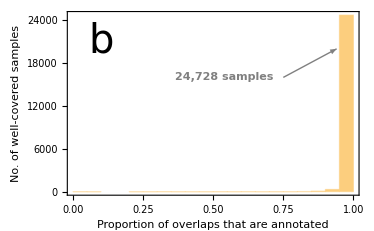

```mathematica
padding={{80,10},{60,12}};fig1b=Show[Histogram[statsBySample[[All,11]]/statsBySample[[All,10]]//N, 15,Frame->True,ImageSize->baseImageSize*.5,BaseStyle->{FontFamily->"Arial",FontSize->15},ImagePadding->padding,FrameLabel->{Style["Proportion of overlaps that are annotated", 15], Style["No. of well-covered samples", 15]}],Graphics[{Gray,Arrow[{{0.75, 16000},{0.94,20000}}],largerLabelForm[ToString[NumberForm[lastBin,DigitBlock->3]]<>" samples", {0.54, 16000}]}],Graphics[{Black, Text[Style["b", FontFamily->"Arial", FontSize->40], {0.1, 21000}]}]]
```

Junctions by sample--->

```mathematica
jxHistList2=HistogramList[statsBySample[[All,7]]/statsBySample[[All,6]],15]
```

{{0,1/20,1/10,3/20,1/5,1/4,3/10,7/20,2/5,9/20,1/2,11/20,3/5,13/20,7/10,3/4,4/5,17/20,9/10,19/20,1},{7,2,3,14,7,17,16,33,50,138,310,625,929,1364,2273,4061,4844,5996,4311,207}}

```mathematica
lessThan80=Total[jxHistList2[[2,Range[1,16]]]]
```

9849

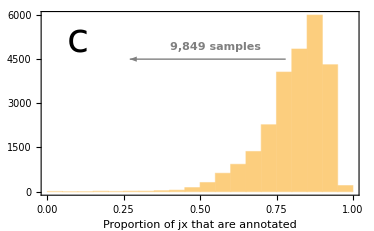

```mathematica
padding2={{75,10},{60,12}};fig1c=Show[Histogram[statsBySample[[All,7]]/statsBySample[[All,6]]//N, 15,Frame->True,ImageSize->baseImageSize*.5,ImagePadding->padding2,BaseStyle->{FontFamily->"Arial",FontSize->15},FrameLabel->{Style["Proportion of jx that are annotated", 15], None}], Graphics[{Gray,Arrow[{{0.78, 4500},{0.27,4500}}], largerLabelForm[ToString[NumberForm[lessThan80,DigitBlock->3]]<>" samples", {0.55, 4900}]}],Graphics[{Black, Text[Style["c", FontFamily->"Arial", FontSize->40], {0.1, 5100}]}]]
```

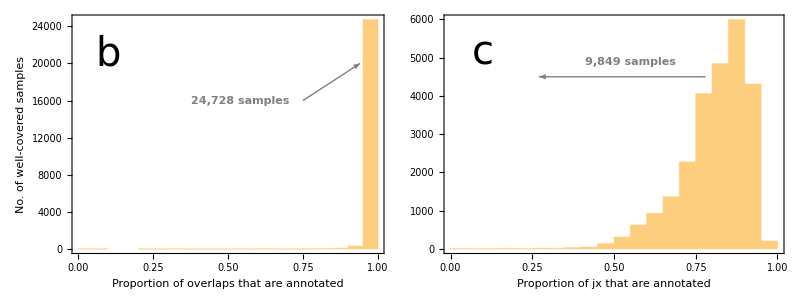
-Graphics-
-Graphics-

```mathematica
fig1=Grid[{{fig1a},{Grid[{{fig1b,fig1c}}]}}]
```

```mathematica
Export["jxannotation.pdf",fig1]
```

jxannotation.pdf

SEQC comparison: subset of 1720 samples out of the 21504 that were aligned by SEQC using magic, rmake, subread. Shows that when a junction is in a lot of samples, it's found by other aligners.

```mathematica
aggregatedJunctionCounts=Drop[Import["hg38.seqc_sample.stats.tsv", "TSV"], 1];
```

```mathematica
totalJunctions = Transpose[Transpose[aggregatedJunctionCounts][[{1,2}]]];oneAlignerJunctions=Transpose[Transpose[aggregatedJunctionCounts][[{1,6}]]];
twoAlignerJunctions=Transpose[Transpose[aggregatedJunctionCounts][[{1,7}]]];
threeAlignerJunctions=Transpose[Transpose[aggregatedJunctionCounts][[{1,8}]]];
```

```mathematica
totalJunctions[[1710-87]]
```

{80,348665}

```mathematica
idx=1710-87
```

1623

```mathematica
atLeastTwoAlignersJunctions = Transpose[{oneAlignerJunctions[[All,1]],threeAlignerJunctions[[All,2]]+twoAlignerJunctions[[All,2]]}];
atLeastOneAlignerJunctions = Transpose[{oneAlignerJunctions[[All,1]],oneAlignerJunctions[[All,2]]+twoAlignerJunctions[[All,2]]+threeAlignerJunctions[[All,2]]}];
```

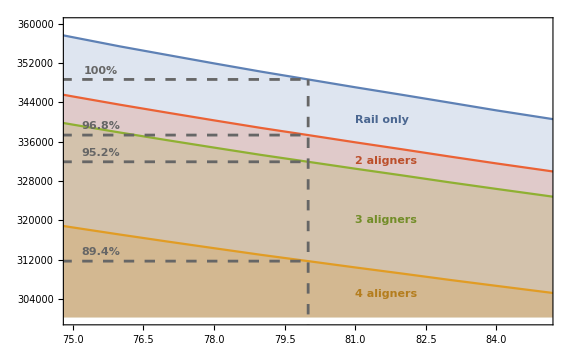

```mathematica
dashedColor=Darker[Gray,0.2];numberStartPos=75.6;insetAnnotationPlot=Show[ListPlot[{totalJunctions,threeAlignerJunctions, atLeastTwoAlignersJunctions, atLeastOneAlignerJunctions}, Joined->True, PlotRange->{{75, 85},{300000,360000}}, Filling->Axis,  Frame->True,ImageSize->Large, BaseStyle->{FontFamily->"Arial",FontSize->15}], Graphics[{Directive[Thickness[0.0035],Dashing[0.013], dashedColor],Line[{{80,0},totalJunctions[[idx]]}],Line[{{0,totalJunctions[[idx]][[2]]},totalJunctions[[idx]]}],Line[{{0,atLeastOneAlignerJunctions[[idx]][[2]]},atLeastOneAlignerJunctions[[idx]]}],
Line[{{0,atLeastTwoAlignersJunctions[[idx]][[2]]},atLeastTwoAlignersJunctions[[idx]]}],Line[{{0,threeAlignerJunctions[[idx]][[2]]},threeAlignerJunctions[[idx]]}],Directive[{Dashing[None],Arrowheads[{-.03,.03}]}], (*Arrow[{{79.63,atLeastOneAlignerJunctions[[idx]][[2]]},{79.63,totalJunctions[[idx]][[2]]}}],bigLabelForm[ToString[NumberForm[N[100-atLeastOneAlignerJunctions[[idx,2]]/totalJunctions[[idx,2]]*100,3],DigitBlock->3]]<>"%",{79.5, 345500}, {1,0}],labelForm[ToString[NumberForm[totalJunctions[[idx,2]]-atLeastOneAlignerJunctions[[idx,2]],DigitBlock->3]]<>" jx", {79.5, 341500},{1,0}],*)labelForm["100%",{numberStartPos,totalJunctions[[idx]][[2]]+1800}],labelForm[ToString[NumberForm[N[atLeastOneAlignerJunctions[[idx,2]]/totalJunctions[[idx,2]]*100,3],DigitBlock->3]]<>"%", {numberStartPos,atLeastOneAlignerJunctions[[idx]][[2]]+1800}],
labelForm[ToString[NumberForm[N[threeAlignerJunctions[[idx,2]]/totalJunctions[[idx,2]]*100,3],DigitBlock->3]]<>"%", {numberStartPos,threeAlignerJunctions[[idx]][[2]]+1800}],
labelForm[ToString[NumberForm[N[atLeastTwoAlignersJunctions[[idx,2]]/totalJunctions[[idx,2]]*100,3],DigitBlock->3]]<>"%", {numberStartPos,atLeastTwoAlignersJunctions[[idx]][[2]]+1800}],(*Directive[Thickness[0.0035],Arrowheads[.035],Dashing[None], dashedColor],Arrow[{{1000,totalJunctions[[idx]][[2]]+41000},{1000,totalJunctions[[idx]][[2]]+100}}],labelForm[ToString[NumberForm[N[100-annotatedJunctions[[idx,2]]/totalJunctions[[idx,2]]*100],3]]<>"% of jx unannotated, but\n"<>ToString[NumberForm[someEvidenceJunctions[[idx,2]]/totalJunctions[[idx,2]]*100//N,3]]<>"% of jx have donor and/or\nacceptor site in annotation", {1005, 330000}, {-1,0}],*)Darker[mathematicaColors[[1]], 0.2],labelForm["Rail only",{81,340500}, {-1,0}],Darker[mathematicaColors[[4]], 0.2],labelForm["2 aligners",{81,332100}, {-1,0}],Darker[mathematicaColors[[3]], 0.2],labelForm["3 aligners",{81,320000}, {-1,0}],Darker[mathematicaColors[[2]], 0.2],labelForm["4 aligners",{81,305000}, {-1,0}]}]]
```

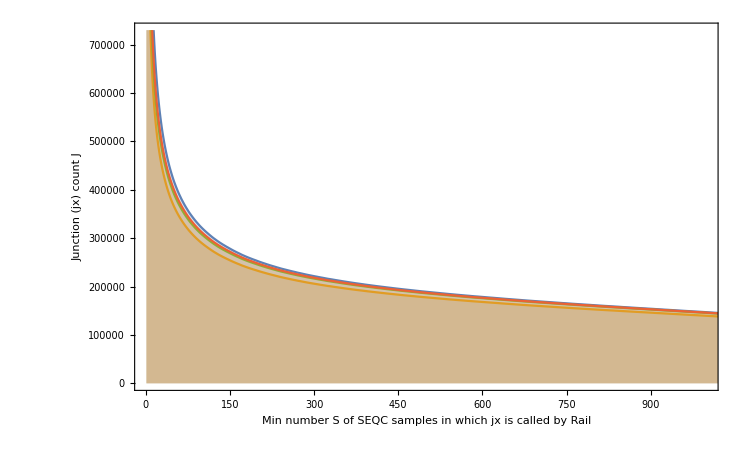

```mathematica
seqcPlot=ListPlot[{totalJunctions,threeAlignerJunctions, atLeastTwoAlignersJunctions,atLeastOneAlignerJunctions}, Joined->True, PlotRange->{{0, 1000},{0,730000}}, Filling->Axis,  Frame->True,ImageSize->baseImageSize, BaseStyle->{FontFamily->"Arial",FontSize->15},Epilog->Inset[insetAnnotationPlot, {625,470000}, Automatic, 700],FrameLabel->{Style["Min number S of SEQC samples in which jx is called by Rail", 22], Style["Junction (jx) count J", 22]}]
```

```mathematica
suppfigseqc=Show[seqcPlot,Graphics[{EdgeForm[Directive[Gray, Thickness[.002]]],Transparent,Rectangle[{75, 300000},{85,360000}]}],Graphics[{Gray,Arrow[{{95,360000},{275,510000}}]}],  Graphics[{Opacity[0.5],Inset[magnifyingGlass,{140,410000},{0,0},50]}],ImageSize->baseImageSize]
```

-Graphics-

```mathematica
Export["seqc.pdf",suppfigseqc]
```

seqc.pdf

Repeat Figure 1a, except at project level for supplement.

```mathematica
aggregatedJunctionCounts=Drop[Import["hg38.project.stats.tsv", "TSV"], 1];
```

```mathematica
totalJunctions = Transpose[Transpose[aggregatedJunctionCounts][[{1,2}]]];annotatedJunctions=Transpose[Transpose[aggregatedJunctionCounts][[{1,3}]]];exonSkipJunctions=Transpose[Transpose[aggregatedJunctionCounts][[{1,4}]]];altStartEndJunctions=Transpose[Transpose[aggregatedJunctionCounts][[{1,5}]]];
novelJunctions=exonSkips=Transpose[Transpose[aggregatedJunctionCounts][[{1,6}]]];
```

```mathematica
exonSkipAnnotatedJunctions = Transpose[{annotatedJunctions[[All,1]],annotatedJunctions[[All,2]]+exonSkipJunctions[[All,2]]}];
someEvidenceJunctions = Transpose[{annotatedJunctions[[All,1]],annotatedJunctions[[All,2]]+exonSkipJunctions[[All,2]]+altStartEndJunctions[[All,2]]}];
```

Introduce levels of evidence, and annotated with junction counts for ≥ 30 samples.

```mathematica
Length[totalJunctions]
```

1844

```mathematica
totalJunctions[[1844-599]]
```

{600,291034}

```mathematica
idx=1844-599
```

1245

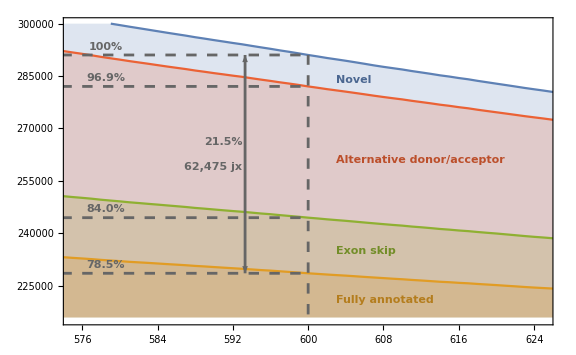

```mathematica
dashedColor=Darker[Gray,0.2];numberStartPos=578.5;adjust=2400;insetAnnotationPlot=Show[ListPlot[{totalJunctions,annotatedJunctions,exonSkipAnnotatedJunctions, someEvidenceJunctions}, Joined->True, PlotRange->{{575, 625},{215500,300000}}, Filling->Axis,  Frame->True,ImageSize->Large, BaseStyle->{FontFamily->"Arial",FontSize->15}], Graphics[{Directive[Thickness[0.0035],Dashing[0.013], dashedColor],Line[{{600,0},totalJunctions[[idx]]}],Line[{{0,totalJunctions[[idx]][[2]]},totalJunctions[[idx]]}],Line[{{0,annotatedJunctions[[idx]][[2]]},annotatedJunctions[[idx]]}],
Line[{{0,exonSkipAnnotatedJunctions[[idx]][[2]]},exonSkipAnnotatedJunctions[[idx]]}],Line[{{0,someEvidenceJunctions[[idx]][[2]]},someEvidenceJunctions[[idx]]}],Directive[{Dashing[None],Arrowheads[{-.05,.05}]}], Arrow[{{593.3,annotatedJunctions[[idx]][[2]]},{593.3,totalJunctions[[idx]][[2]]}}],bigLabelForm[ToString[NumberForm[N[100-annotatedJunctions[[idx,2]]/totalJunctions[[idx,2]]*100,3],DigitBlock->3]]<>"%",{593, 266000}, {1,0}],labelForm[ToString[NumberForm[totalJunctions[[idx,2]]-annotatedJunctions[[idx,2]],DigitBlock->3]]<>" jx", {593, 259000},{1,0}],labelForm["100%",{numberStartPos,totalJunctions[[idx]][[2]]+adjust}],labelForm[ToString[NumberForm[N[someEvidenceJunctions[[idx,2]]/totalJunctions[[idx,2]]*100,3],DigitBlock->3]]<>"%", {numberStartPos,someEvidenceJunctions[[idx]][[2]]+adjust}],
labelForm[ToString[NumberForm[N[annotatedJunctions[[idx,2]]/totalJunctions[[idx,2]]*100,3],DigitBlock->3]]<>"%", {numberStartPos,annotatedJunctions[[idx]][[2]]+adjust}],
labelForm[ToString[NumberForm[N[exonSkipAnnotatedJunctions[[idx,2]]/totalJunctions[[idx,2]]*100,3],DigitBlock->3]]<>"%", {numberStartPos,exonSkipAnnotatedJunctions[[idx]][[2]]+adjust}],Darker[mathematicaColors[[1]], 0.2],labelForm["Novel",{603,284000}, {-1,0}],Darker[mathematicaColors[[4]], 0.2],labelForm["Alternative donor/acceptor",{603,261000}, {-1,0}],Darker[mathematicaColors[[3]], 0.2],labelForm["Exon skip",{603,235000}, {-1,0}],Darker[mathematicaColors[[2]], 0.2],labelForm["Fully annotated",{603,221000}, {-1,0}]}]]
```

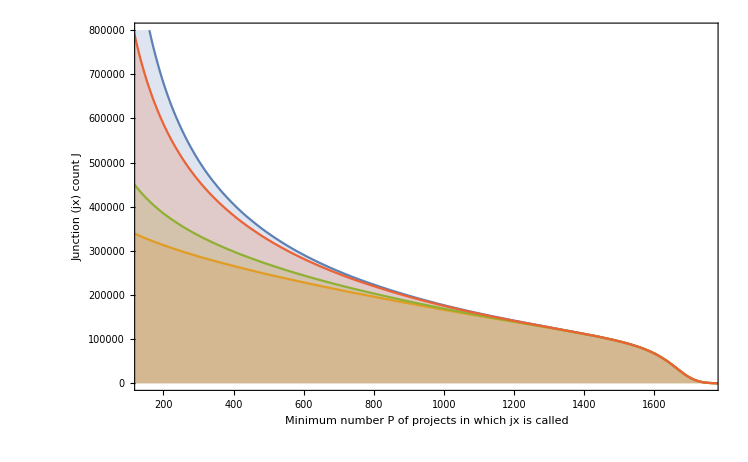

```mathematica
bigAnnotationPlot=ListPlot[{totalJunctions,annotatedJunctions,Transpose[{Transpose[annotatedJunctions][[1]],Transpose[annotatedJunctions][[2]]+Transpose[exonSkipJunctions][[2]]}], Transpose[{Transpose[annotatedJunctions][[1]],Transpose[annotatedJunctions][[2]]+Transpose[exonSkipJunctions][[2]]+Transpose[altStartEndJunctions][[2]]}]}, Joined->True, PlotRange->{{150, 1750},{0,800000}}, Filling->Axis,  Frame->True,ImageSize->baseImageSize, BaseStyle->{FontFamily->"Arial",FontSize->15},Epilog->Inset[insetAnnotationPlot, {1175,520000}, Automatic, 1060],FrameLabel->{Style["Minimum number P of projects in which jx is called",22], Style["Junction (jx) count J",22]}]
```

```mathematica
magFlipped=Import["magflipped.png"]
```

-Graphics-

```mathematica
suppfigproj=Show[bigAnnotationPlot,Graphics[{EdgeForm[Directive[Gray, Thickness[.0015]]],Transparent,Rectangle[{575, 215500},{625,300000}]}],Graphics[{Gray,Arrow[BezierCurve[{{600,310000},{505,420000},{635,480000}}]]}],  Graphics[{Opacity[0.5],Inset[magFlipped,{547,355000},{0,0},80]}],ImageSize->baseImageSize]
```

-Graphics-

```mathematica
Export["projlevel.pdf",suppfigproj]
```

projlevel.pdf

For how many runs are we missing Biosample submission dates? We ran the command
cat ../intropolis.v2.hg38.tsv.gz | grep -vwFf <(cat biosample_tags.tsv | cut-f10 | tail-n+2) >missing_biosample_dates.tsv
in the sra/v2/hg38 directory of the repo nellore/runs to obtain that dates were missing for 986/~50k ~ 2% of runs. Our analysis is reasonably complete if we ignore them.

```mathematica
junctionsEvidenceVsDatesGeq40=Drop[Import["!gzip -cd hg38.sample_count_submission_date_overlap_geq_40.tsv.gz", "TSV"], 1];
```

```mathematica
junctionsEvidenceVsDatesGeq[x_, y_:junctionsEvidenceVsDatesGeq40]:= Select[y,#[[1]]≥x &];talliedJunctionsGeq[x_,y_:junctionsEvidenceVsDatesGeq40]:=SortBy[Tally[junctionsEvidenceVsDatesGeq[x, y][[All,4]]], First];accumulatedJunctionsGeq[x_, y_:junctionsEvidenceVsDatesGeq40]:=(talliedJunctions=talliedJunctionsGeq[x, y];Transpose[{talliedJunctions[[All,1]],Accumulate[talliedJunctions[[All,2]]]}])
```

Convert from days after 2/27/2009 to dates.

```mathematica
Clear[daysToDate]
```

```mathematica
daysToDate[x_] :=DatePlus[DateObject[{2009, 02, 27}], x]
```

When were junctions supported by reads in ≥ 40, 80, 160, 320 reads across samples found?

```mathematica
twentyThirteen=1404;daysToDate[twentyThirteen]
```

Tue 1 Jan 2013

```mathematica
dateFormat={"Month","/","Day","/","YearShort"};
```

Design ticks to intersect 1/1/2013.

```mathematica
dateTicks=({#,DateString[daysToDate[#], dateFormat]}&/@Range[0, 2500, 234])
```

{{0,02/27/09},{234,10/19/09},{468,06/10/10},{702,01/30/11},{936,09/21/11},{1170,05/12/12},{1404,01/01/13},{1638,08/23/13},{1872,04/14/14},{2106,12/04/14},{2340,07/26/15}}

```mathematica
lastDay=Max[junctionsEvidenceVsDatesGeq40[[All,4]]]
```

2531

```mathematica
dateTicks=Append[dateTicks, {lastDay,DateString[daysToDate[lastDay], dateFormat]}]
```

{{0,02/27/09},{234,10/19/09},{468,06/10/10},{702,01/30/11},{936,09/21/11},{1170,05/12/12},{1404,01/01/13},{1638,08/23/13},{1872,04/14/14},{2106,12/04/14},{2340,07/26/15},{2531,02/02/16}}

```mathematica
baseJunctionsPlotData= accumulatedJunctionsGeq/@{40,320, 160,80};
```

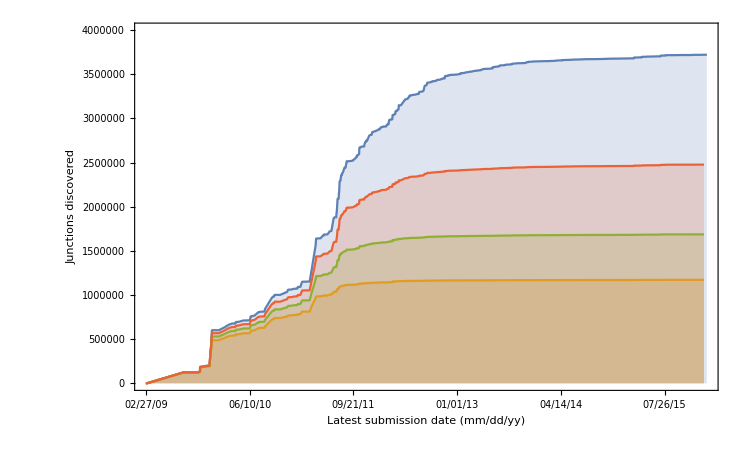

```mathematica
baseJunctionsPlot=ListPlot[baseJunctionsPlotData, Joined->True,Filling->Axis, Frame->True, FrameTicks->{{Automatic,None},{dateTicks, None}},BaseStyle->{FontFamily->"Arial",FontSize->12}, FrameLabel->{Style["Latest submission date (mm/dd/yy)", 22], Style["Junctions discovered", 22]}, ImageSize->baseImageSize, PlotRange->{All, {0, 4*10^6}}]
```

```mathematica
sortedDays= Sort[junctionsEvidenceVsDatesGeq40[[All,4]]];
```

```mathematica
junctionsInCommons=Count[sortedDays, #]&/@Commonest[sortedDays,7]
```

{123621,203526,186631,134084,278210,141545,158676}

These correspond to, respectively....

```mathematica
Commonest[sortedDays,7]
```

{170,293,298,748,766,847,865}

```mathematica
daysToDate/@Commonest[sortedDays,7]
```

{Sun 16 Aug 2009,Thu 17 Dec 2009,Tue 22 Dec 2009,Thu 17 Mar 2011,Mon 4 Apr 2011,Fri 24 Jun 2011,Tue 12 Jul 2011}

Some of these dates correspond to jumps in the plot above. Grepping for the submission dates in biosample_tags.tsv in sra/v2/hg38 gives samples in the following projects:
1. who cares
2. Study of 69 LCLs (2)(Understanding mechanisms underlying human gene expression variation with RNA sequencing, by Pickrell et al.) (SRP001540) 17 Dec 2009
3. Study of 41 Coriell cell lines (SRP001563)(Polymorphic cis-and trans-regulation of human gene expression, by Cheung et al.) 22 Dec 2009
4. Illumina bodyMap2 (ERP000546) 17-Mar-2011
5. University of Washington Human Reference Epigenome Mapping Project (SRP001371)(total RNA, fetal tissues, contributed most junctions on a single day (4 April 2011)); note also that on this day, there are two more projects: SRP005309, a microRNA study with negligible # junctions, and SRP005846, for which grepping hg38.stats_by_sample.tsv gives ~95 annotated jx, < 50k each of 4 samples. So overwhelmingly dominant contribution on 4 April 2011 is UW.
6. 2 different projects:SRP018008 and SRP020237. Not at all clear that either was dominant contribution, so exclude.
7. ENCODE long RNA-seq from CSHL (SRP007461) 12-Jul-2011

Annotate plot with the top 4 projects.
1. UWE
2. Pic
3. Che
4. ENC

bodyMap 2 is interesting in that GENCODE incorporated it in its annotation, so include it.

Find GEUVADIS. Grepping biosample_tags.tsv gives that the GEUVADIS submission date was 2012-11-07. This was

```mathematica
daysToDate[1349]
```

Wed 7 Nov 2012

A glance at the tallies below shows that just 22,862 novel junctions were contributed on the day GEUVADIS samples were submitted to Biosample!

```mathematica
tallied=Tally[sortedDays]
```

{{0,1095},{7,619},{170,123621},{237,47},{244,10380},{245,50961},{278,13419},{287,8},{293,203526},{294,11019},{298,186631},{329,53},{356,34218},{362,9983},{376,20875},{382,2988},{388,7719},{398,6},{403,86},{406,16555},{409,1},{411,1862},{418,48},{440,16140},{448,264},{454,653},{469,1597},{473,44214},{474,15},{490,8522},{508,38976},{511,7},{515,3985},{525,1677},{535,1312},{538,30137},{566,116698},{573,21827},{578,732},{581,19355},{606,48},{637,33552},{642,24819},{648,1520},{654,33},{671,9754},{677,465},{679,838},{684,2562},{686,16369},{697,28},{705,58841},{718,720},{739,1642},{748,134084},{766,278210},{768,74416},{788,3083},{791,8399},{795,12086},{798,6651},{801,1749},{803,13268},{819,1866},{824,15390},{829,19371},{837,3411},{847,141545},{851,13493},{859,845},{860,46203},{861,3645},{865,158676},{870,1662},{871,66723},{872,1759},{874,123597},{877,11546},{878,310},{881,59646},{882,2128},{884,855},{885,18417},{886,4632},{889,7193},{896,54352},{901,592},{906,72330},{910,20},{921,1729},{930,3646},{935,4290},{936,1},{937,5913},{943,14893},{945,1057},{950,14968},{951,335},{952,18589},{956,559},{959,11548},{962,3572},{963,63964},{965,12679},{969,576},{970,986},{971,1666},{972,4159},{974,1642},{985,496},{986,24311},{990,25649},{993,2106},{994,13537},{998,60},{1007,52264},{1008,4406},{1011,6460},{1014,2802},{1015,84},{1018,752},{1019,842},{1021,27692},{1022,2490},{1033,7895},{1035,1281},{1036,4180},{1043,5051},{1047,7178},{1049,3433},{1054,125},{1055,7530},{1056,1},{1057,2423},{1059,11102},{1061,3928},{1067,1133},{1069,6854},{1070,7},{1081,566},{1084,933},{1089,22794},{1092,2},{1095,2634},{1096,22181},{1097,11433},{1098,12888},{1099,1998},{1102,3371},{1104,466},{1106,159},{1109,4},{1112,4528},{1113,46275},{1116,333},{1118,1271},{1119,5084},{1120,1238},{1124,848},{1125,1834},{1126,30824},{1129,5076},{1132,64},{1133,86},{1134,9505},{1140,8529},{1141,46168},{1145,1},{1146,105},{1151,271},{1166,52824},{1169,12476},{1174,2376},{1175,752},{1180,5940},{1181,687},{1182,9},{1183,5374},{1188,17053},{1189,228},{1190,12175},{1193,147},{1195,3594},{1197,269},{1200,352},{1202,216},{1207,4002},{1208,591},{1209,397},{1214,19},{1215,59},{1222,6263},{1224,913},{1225,433},{1228,5},{1230,412},{1231,41},{1232,19073},{1236,5764},{1238,37},{1239,700},{1242,152},{1243,737},{1244,11},{1245,780},{1250,3120},{1253,7383},{1257,47546},{1258,6146},{1263,5619},{1264,1063},{1265,317},{1267,5151},{1270,25105},{1277,1044},{1279,57},{1281,1711},{1285,2409},{1286,3},{1287,1053},{1288,4383},{1289,133},{1290,448},{1291,451},{1292,263},{1293,9},{1294,125},{1295,3882},{1296,40},{1299,51},{1300,1312},{1301,1002},{1302,77},{1305,115},{1307,228},{1308,515},{1309,469},{1313,10492},{1315,72},{1316,564},{1321,793},{1326,1493},{1327,665},{1330,3761},{1333,1490},{1334,1649},{1335,483},{1337,2450},{1339,2374},{1340,163},{1344,100},{1348,735},{1349,22862},{1350,339},{1351,4233},{1352,62},{1357,589},{1361,541},{1362,3621},{1364,2490},{1365,212},{1369,1},{1370,48},{1371,4982},{1372,213},{1376,247},{1379,917},{1386,297},{1387,309},{1388,81},{1389,202},{1392,122},{1393,861},{1394,8},{1398,339},{1399,2},{1400,414},{1405,1068},{1406,27},{1407,1528},{1410,438},{1411,189},{1413,2598},{1417,77},{1418,1695},{1419,20},{1420,8243},{1421,2},{1425,24},{1428,227},{1431,2280},{1433,27},{1435,41},{1436,1039},{1439,557},{1443,5000},{1446,41},{1447,1295},{1452,562},{1453,16},{1456,1357},{1459,4181},{1461,138},{1463,16},{1469,618},{1475,3935},{1476,1219},{1477,14},{1480,1315},{1482,1696},{1484,971},{1485,14},{1487,381},{1488,403},{1495,1456},{1496,1709},{1497,56},{1498,95},{1501,41},{1502,1108},{1503,911},{1508,351},{1510,331},{1512,4385},{1516,2191},{1517,1984},{1518,1795},{1522,1377},{1523,636},{1524,1025},{1526,850},{1529,1248},{1531,51},{1533,155},{1537,2},{1539,401},{1540,208},{1541,1},{1543,441},{1545,240},{1546,46},{1551,254},{1552,471},{1553,28},{1556,419},{1557,630},{1558,530},{1559,95},{1560,404},{1561,527},{1564,87},{1565,12923},{1567,747},{1568,1096},{1571,2299},{1574,40},{1575,218},{1578,123},{1579,1821},{1580,535},{1581,199},{1582,415},{1585,88},{1586,45},{1587,771},{1588,31},{1589,1},{1592,2662},{1594,32},{1595,5451},{1596,1211},{1597,404},{1599,3139},{1600,146},{1601,94},{1602,7},{1603,10},{1606,44},{1607,696},{1608,28},{1610,65},{1612,10},{1613,325},{1614,330},{1615,81},{1617,132},{1621,2005},{1622,164},{1623,3490},{1627,34},{1628,498},{1629,1260},{1634,167},{1636,420},{1640,20},{1642,564},{1643,630},{1644,25},{1645,138},{1646,65},{1648,13},{1649,204},{1650,283},{1651,22},{1652,6155},{1655,50},{1656,185},{1657,1595},{1659,1},{1660,43},{1663,1028},{1665,613},{1670,700},{1672,12},{1673,1287},{1676,140},{1678,817},{1693,1},{1694,528},{1697,608},{1698,9},{1699,35},{1701,166},{1704,12},{1705,18},{1707,31},{1708,90},{1711,60},{1712,1229},{1713,230},{1714,4021},{1715,328},{1718,4002},{1719,12},{1721,54},{1722,61},{1725,373},{1726,4025},{1727,3},{1728,244},{1729,600},{1730,2},{1733,54},{1736,128},{1738,12},{1740,78},{1741,23},{1743,77},{1744,1900},{1746,32},{1747,451},{1748,426},{1750,30},{1751,73},{1752,39},{1753,19},{1754,48},{1755,128},{1756,60},{1757,53},{1760,3},{1761,159},{1763,251},{1767,314},{1770,453},{1772,2},{1774,2},{1775,1},{1776,59},{1777,14},{1778,55},{1780,2},{1781,121},{1782,544},{1783,50},{1784,117},{1785,11},{1787,23},{1790,26},{1791,348},{1792,3},{1795,54},{1796,308},{1797,124},{1799,13},{1802,1},{1803,63},{1805,263},{1806,108},{1809,38},{1810,9},{1811,36},{1812,146},{1813,13},{1817,1},{1818,10},{1819,11},{1820,15},{1821,2},{1822,1},{1823,54},{1824,52},{1825,1274},{1827,15},{1829,9},{1830,222},{1831,26},{1832,1},{1834,264},{1837,173},{1838,75},{1840,502},{1841,141},{1842,61},{1844,19},{1845,214},{1846,108},{1847,247},{1848,230},{1849,559},{1850,877},{1851,1273},{1852,44},{1853,94},{1854,104},{1855,31},{1858,4},{1859,177},{1860,216},{1861,63},{1862,132},{1865,201},{1866,460},{1867,26},{1868,175},{1869,13},{1872,55},{1873,47},{1874,22},{1875,18},{1876,77},{1879,18},{1880,3541},{1881,30},{1884,31},{1885,2},{1886,20},{1887,188},{1888,4},{1889,8},{1890,24},{1892,163},{1893,48},{1894,201},{1895,186},{1896,120},{1897,503},{1900,41},{1901,14},{1902,10},{1904,196},{1907,3},{1908,15},{1909,316},{1910,143},{1911,1},{1913,3},{1914,2},{1915,62},{1917,3},{1918,799},{1921,574},{1923,131},{1924,75},{1926,2},{1928,20},{1929,1155},{1930,297},{1931,40},{1933,199},{1935,38},{1936,29},{1937,163},{1938,82},{1939,19},{1942,58},{1945,9},{1946,10},{1949,89},{1950,125},{1951,6},{1952,740},{1955,12},{1956,26},{1957,49},{1959,190},{1960,34},{1962,17},{1963,13},{1964,8},{1965,5},{1966,69},{1967,1},{1968,1},{1970,62},{1971,62},{1972,34},{1974,18},{1975,1922},{1977,31},{1978,3},{1979,7},{1980,33},{1981,1},{1983,36},{1984,54},{1985,5},{1986,14},{1987,55},{1988,13},{1989,11},{1990,30},{1991,15},{1992,45},{1993,30},{1994,31},{1997,1},{1998,44},{1999,16},{2000,180},{2001,21},{2002,24},{2005,6},{2006,11},{2007,25},{2008,35},{2009,36},{2010,4},{2012,2},{2013,14},{2014,40},{2015,6},{2016,12},{2018,2},{2019,7},{2021,2},{2022,157},{2023,26},{2026,5},{2027,243},{2028,5},{2029,23},{2030,2},{2033,24},{2034,2},{2035,2},{2036,7},{2037,90},{2040,1},{2041,2},{2042,104},{2043,30},{2045,8},{2047,150},{2048,45},{2049,316},{2050,102},{2051,71},{2053,15},{2055,2},{2057,29},{2058,6},{2061,27},{2062,522},{2063,1},{2064,8},{2065,5},{2069,65},{2070,1019},{2071,35},{2072,2},{2073,8},{2074,2},{2075,26},{2076,30},{2077,5},{2078,98},{2079,1},{2080,3},{2081,4},{2082,2},{2083,73},{2084,1119},{2085,37},{2086,34},{2089,19},{2090,45},{2091,24},{2092,3},{2093,113},{2096,14},{2097,66},{2100,13},{2103,8},{2104,30},{2105,93},{2106,23},{2107,5},{2110,53},{2111,334},{2113,33},{2114,30},{2117,40},{2119,13},{2120,67},{2121,16},{2124,31},{2126,6},{2131,23},{2132,22},{2133,107},{2138,13},{2139,3},{2140,28},{2141,605},{2142,63},{2146,69},{2147,4},{2148,56},{2153,20},{2154,1},{2155,165},{2156,46},{2159,15},{2160,20},{2161,59},{2162,94},{2163,472},{2166,47},{2167,18},{2168,18},{2169,246},{2170,83},{2173,4},{2174,105},{2175,2},{2176,1},{2177,5},{2181,20},{2182,171},{2184,35},{2186,3},{2187,21},{2188,6},{2189,22},{2190,5},{2191,53},{2194,20},{2195,31},{2196,82},{2197,15},{2198,35},{2201,9},{2202,356},{2203,9090},{2204,87},{2205,5},{2207,26},{2208,41},{2210,285},{2211,19},{2212,33},{2213,90},{2215,9},{2216,14},{2217,21},{2218,34},{2222,413},{2223,24},{2224,115},{2225,44},{2230,4},{2231,23},{2233,8},{2235,1},{2236,27},{2237,2},{2238,6672},{2239,14},{2243,10},{2244,320},{2245,6},{2246,9},{2247,155},{2251,4},{2252,4},{2253,1},{2254,80},{2257,7},{2258,1},{2259,5},{2260,2064},{2261,10},{2264,7},{2265,2},{2266,38},{2267,41},{2268,3},{2271,90},{2272,17},{2274,2},{2275,18},{2279,21},{2280,24},{2281,2},{2282,45},{2283,67},{2285,20},{2286,201},{2287,842},{2288,5},{2289,13},{2292,13},{2293,3},{2294,2},{2295,58},{2296,7},{2299,627},{2300,2},{2302,2},{2303,5},{2304,3},{2305,102},{2306,174},{2307,2},{2313,45},{2315,2},{2316,1},{2320,4},{2321,72},{2322,11},{2324,9040},{2330,18},{2332,1},{2333,5},{2334,1},{2335,1},{2336,1},{2337,8},{2338,5},{2339,3},{2341,2},{2342,16},{2343,4},{2344,4},{2345,3896},{2348,19},{2350,444},{2352,28},{2355,6},{2356,15},{2358,1},{2364,13},{2365,1},{2369,4},{2373,2},{2379,59},{2380,3},{2383,2},{2384,38},{2386,2},{2387,5},{2390,3},{2391,9},{2392,1},{2393,464},{2394,7},{2397,1},{2399,4},{2400,13},{2404,3},{2405,6},{2407,674},{2408,8},{2411,33},{2412,8},{2414,1},{2415,3},{2417,2},{2420,7},{2422,3},{2426,3},{2427,1},{2434,3},{2435,1},{2436,3},{2439,8},{2440,16},{2441,31},{2442,3},{2445,2},{2447,10},{2450,2},{2455,8},{2456,1},{2457,1},{2460,228},{2464,6},{2468,1916},{2469,6},{2470,5},{2476,1},{2480,1},{2484,188},{2485,7},{2488,41},{2499,8},{2502,1},{2509,5},{2510,18},{2513,863},{2518,62},{2523,3},{2531,2}}

Find GEUV day's rank:

```mathematica
Reverse[SortBy[tallied, Last]]
```

{{766,278210},{293,203526},{298,186631},{865,158676},{847,141545},{748,134084},{170,123621},{874,123597},{566,116698},{768,74416},{906,72330},{871,66723},{963,63964},{881,59646},{705,58841},{896,54352},{1166,52824},{1007,52264},{245,50961},{1257,47546},{1113,46275},{860,46203},{1141,46168},{473,44214},{508,38976},{356,34218},{637,33552},{1126,30824},{538,30137},{1021,27692},{990,25649},{1270,25105},{642,24819},{986,24311},{1349,22862},{1089,22794},{1096,22181},{573,21827},{376,20875},{829,19371},{581,19355},{1232,19073},{952,18589},{885,18417},{1188,17053},{406,16555},{686,16369},{440,16140},{824,15390},{950,14968},{943,14893},{994,13537},{851,13493},{278,13419},{803,13268},{1565,12923},{1098,12888},{965,12679},{1169,12476},{1190,12175},{795,12086},{959,11548},{877,11546},{1097,11433},{1059,11102},{294,11019},{1313,10492},{244,10380},{362,9983},{671,9754},{1134,9505},{2203,9090},{2324,9040},{1140,8529},{490,8522},{791,8399},{1420,8243},{1033,7895},{388,7719},{1055,7530},{1253,7383},{889,7193},{1047,7178},{1069,6854},{2238,6672},{798,6651},{1011,6460},{1222,6263},{1652,6155},{1258,6146},{1180,5940},{937,5913},{1236,5764},{1263,5619},{1595,5451},{1183,5374},{1267,5151},{1119,5084},{1129,5076},{1043,5051},{1443,5000},{1371,4982},{886,4632},{1112,4528},{1008,4406},{1512,4385},{1288,4383},{935,4290},{1351,4233},{1459,4181},{1036,4180},{972,4159},{1726,4025},{1714,4021},{1718,4002},{1207,4002},{515,3985},{1475,3935},{1061,3928},{2345,3896},{1295,3882},{1330,3761},{930,3646},{861,3645},{1362,3621},{1195,3594},{962,3572},{1880,3541},{1623,3490},{1049,3433},{837,3411},{1102,3371},{1599,3139},{1250,3120},{788,3083},{382,2988},{1014,2802},{1592,2662},{1095,2634},{1413,2598},{684,2562},{1364,2490},{1022,2490},{1337,2450},{1057,2423},{1285,2409},{1174,2376},{1339,2374},{1571,2299},{1431,2280},{1516,2191},{882,2128},{993,2106},{2260,2064},{1621,2005},{1099,1998},{1517,1984},{1975,1922},{2468,1916},{1744,1900},{819,1866},{411,1862},{1125,1834},{1579,1821},{1518,1795},{872,1759},{801,1749},{921,1729},{1281,1711},{1496,1709},{1482,1696},{1418,1695},{525,1677},{971,1666},{870,1662},{1334,1649},{974,1642},{739,1642},{469,1597},{1657,1595},{1407,1528},{648,1520},{1326,1493},{1333,1490},{1495,1456},{1522,1377},{1456,1357},{1480,1315},{1300,1312},{535,1312},{1447,1295},{1673,1287},{1035,1281},{1825,1274},{1851,1273},{1118,1271},{1629,1260},{1529,1248},{1120,1238},{1712,1229},{1476,1219},{1596,1211},{1929,1155},{1067,1133},{2084,1119},{1502,1108},{1568,1096},{0,1095},{1405,1068},{1264,1063},{945,1057},{1287,1053},{1277,1044},{1436,1039},{1663,1028},{1524,1025},{2070,1019},{1301,1002},{970,986},{1484,971},{1084,933},{1379,917},{1224,913},{1503,911},{1850,877},{2513,863},{1393,861},{884,855},{1526,850},{1124,848},{859,845},{2287,842},{1019,842},{679,838},{1678,817},{1918,799},{1321,793},{1245,780},{1587,771},{1175,752},{1018,752},{1567,747},{1952,740},{1243,737},{1348,735},{578,732},{718,720},{1670,700},{1239,700},{1607,696},{1181,687},{2407,674},{1327,665},{454,653},{1523,636},{1643,630},{1557,630},{2299,627},{7,619},{1469,618},{1665,613},{1697,608},{2141,605},{1729,600},{901,592},{1208,591},{1357,589},{969,576},{1921,574},{1081,566},{1642,564},{1316,564},{1452,562},{1849,559},{956,559},{1439,557},{1782,544},{1361,541},{1580,535},{1558,530},{1694,528},{1561,527},{2062,522},{1308,515},{1897,503},{1840,502},{1628,498},{985,496},{1335,483},{2163,472},{1552,471},{1309,469},{1104,466},{677,465},{2393,464},{1866,460},{1770,453},{1747,451},{1291,451},{1290,448},{2350,444},{1543,441},{1410,438},{1225,433},{1748,426},{1636,420},{1556,419},{1582,415},{1400,414},{2222,413},{1230,412},{1597,404},{1560,404},{1488,403},{1539,401},{1209,397},{1487,381},{1725,373},{2202,356},{1200,352},{1508,351},{1791,348},{1398,339},{1350,339},{951,335},{2111,334},{1116,333},{1510,331},{1614,330},{1715,328},{1613,325},{2244,320},{1265,317},{2049,316},{1909,316},{1767,314},{878,310},{1387,309},{1796,308},{1930,297},{1386,297},{2210,285},{1650,283},{1151,271},{1197,269},{1834,264},{448,264},{1805,263},{1292,263},{1551,254},{1763,251},{1847,247},{1376,247},{2169,246},{1728,244},{2027,243},{1545,240},{1848,230},{1713,230},{2460,228},{1307,228},{1189,228},{1428,227},{1830,222},{1575,218},{1860,216},{1202,216},{1845,214},{1372,213},{1365,212},{1540,208},{1649,204},{1389,202},{2286,201},{1894,201},{1865,201},{1933,199},{1581,199},{1904,196},{1959,190},{1411,189},{2484,188},{1887,188},{1895,186},{1656,185},{2000,180},{1859,177},{1868,175},{2306,174},{1837,173},{2182,171},{1634,167},{1701,166},{2155,165},{1622,164},{1937,163},{1892,163},{1340,163},{1761,159},{1106,159},{2022,157},{2247,155},{1533,155},{1242,152},{2047,150},{1193,147},{1812,146},{1600,146},{1910,143},{1841,141},{1676,140},{1645,138},{1461,138},{1289,133},{1862,132},{1617,132},{1923,131},{1755,128},{1736,128},{1950,125},{1294,125},{1054,125},{1797,124},{1578,123},{1392,122},{1781,121},{1896,120},{1784,117},{2224,115},{1305,115},{2093,113},{1846,108},{1806,108},{2133,107},{2174,105},{1146,105},{2042,104},{1854,104},{2305,102},{2050,102},{1344,100},{2078,98},{1559,95},{1498,95},{2162,94},{1853,94},{1601,94},{2105,93},{2271,90},{2213,90},{2037,90},{1708,90},{1949,89},{1585,88},{2204,87},{1564,87},{1133,86},{403,86},{1015,84},{2170,83},{2196,82},{1938,82},{1615,81},{1388,81},{2254,80},{1740,78},{1876,77},{1743,77},{1417,77},{1302,77},{1924,75},{1838,75},{2083,73},{1751,73},{2321,72},{1315,72},{2051,71},{2146,69},{1966,69},{2283,67},{2120,67},{2097,66},{2069,65},{1646,65},{1610,65},{1132,64},{2142,63},{1861,63},{1803,63},{2518,62},{1971,62},{1970,62},{1915,62},{1352,62},{1842,61},{1722,61},{1756,60},{1711,60},{998,60},{2379,59},{2161,59},{1776,59},{1215,59},{2295,58},{1942,58},{1279,57},{2148,56},{1497,56},{1987,55},{1872,55},{1778,55},{1984,54},{1823,54},{1795,54},{1733,54},{1721,54},{2191,53},{2110,53},{1757,53},{329,53},{1824,52},{1531,51},{1299,51},{1783,50},{1655,50},{1957,49},{1893,48},{1754,48},{1370,48},{606,48},{418,48},{2166,47},{1873,47},{237,47},{2156,46},{1546,46},{2313,45},{2282,45},{2090,45},{2048,45},{1992,45},{1586,45},{2225,44},{1998,44},{1852,44},{1606,44},{1660,43},{2488,41},{2267,41},{2208,41},{1900,41},{1501,41},{1446,41},{1435,41},{1231,41},{2117,40},{2014,40},{1931,40},{1574,40},{1296,40},{1752,39},{2384,38},{2266,38},{1935,38},{1809,38},{2085,37},{1238,37},{2009,36},{1983,36},{1811,36},{2198,35},{2184,35},{2071,35},{2008,35},{1699,35},{2218,34},{2086,34},{1972,34},{1960,34},{1627,34},{2411,33},{2212,33},{2113,33},{1980,33},{654,33},{1746,32},{1594,32},{2441,31},{2195,31},{2124,31},{1994,31},{1977,31},{1884,31},{1855,31},{1707,31},{1588,31},{2114,30},{2104,30},{2076,30},{2043,30},{1993,30},{1990,30},{1881,30},{1750,30},{2057,29},{1936,29},{2352,28},{2140,28},{1608,28},{1553,28},{697,28},{2236,27},{2061,27},{1433,27},{1406,27},{2207,26},{2075,26},{2023,26},{1956,26},{1867,26},{1831,26},{1790,26},{2007,25},{1644,25},{2280,24},{2223,24},{2091,24},{2033,24},{2002,24},{1890,24},{1425,24},{2231,23},{2131,23},{2106,23},{2029,23},{1787,23},{1741,23},{2189,22},{2132,22},{1874,22},{1651,22},{2279,21},{2217,21},{2187,21},{2001,21},{2285,20},{2194,20},{2181,20},{2160,20},{2153,20},{1928,20},{1886,20},{1640,20},{1419,20},{910,20},{2348,19},{2211,19},{2089,19},{1939,19},{1844,19},{1753,19},{1214,19},{2510,18},{2330,18},{2275,18},{2168,18},{2167,18},{1974,18},{1879,18},{1875,18},{1705,18},{2272,17},{1962,17},{2440,16},{2342,16},{2121,16},{1999,16},{1463,16},{1453,16},{2356,15},{2197,15},{2159,15},{2053,15},{1991,15},{1908,15},{1827,15},{1820,15},{474,15},{2239,14},{2216,14},{2096,14},{2013,14},{1986,14},{1901,14},{1777,14},{1485,14},{1477,14},{2400,13},{2364,13},{2292,13},{2289,13},{2138,13},{2119,13},{2100,13},{1988,13},{1963,13},{1869,13},{1813,13},{1799,13},{1648,13},{2016,12},{1955,12},{1738,12},{1719,12},{1704,12},{1672,12},{2322,11},{2006,11},{1989,11},{1819,11},{1785,11},{1244,11},{2447,10},{2261,10},{2243,10},{1946,10},{1902,10},{1818,10},{1612,10},{1603,10},{2391,9},{2246,9},{2215,9},{2201,9},{1945,9},{1829,9},{1810,9},{1698,9},{1293,9},{1182,9},{2499,8},{2455,8},{2439,8},{2412,8},{2408,8},{2337,8},{2233,8},{2103,8},{2073,8},{2064,8},{2045,8},{1964,8},{1889,8},{1394,8},{287,8},{2485,7},{2420,7},{2394,7},{2296,7},{2264,7},{2257,7},{2036,7},{2019,7},{1979,7},{1602,7},{1070,7},{511,7},{2469,6},{2464,6},{2405,6},{2355,6},{2245,6},{2188,6},{2126,6},{2058,6},{2015,6},{2005,6},{1951,6},{398,6},{2509,5},{2470,5},{2387,5},{2338,5},{2333,5},{2303,5},{2288,5},{2259,5},{2205,5},{2190,5},{2177,5},{2107,5},{2077,5},{2065,5},{2028,5},{2026,5},{1985,5},{1965,5},{1228,5},{2399,4},{2369,4},{2344,4},{2343,4},{2320,4},{2252,4},{2251,4},{2230,4},{2173,4},{2147,4},{2081,4},{2010,4},{1888,4},{1858,4},{1109,4},{2523,3},{2442,3},{2436,3},{2434,3},{2426,3},{2422,3},{2415,3},{2404,3},{2390,3},{2380,3},{2339,3},{2304,3},{2293,3},{2268,3},{2186,3},{2139,3},{2092,3},{2080,3},{1978,3},{1917,3},{1913,3},{1907,3},{1792,3},{1760,3},{1727,3},{1286,3},{2531,2},{2450,2},{2445,2},{2417,2},{2386,2},{2383,2},{2373,2},{2341,2},{2315,2},{2307,2},{2302,2},{2300,2},{2294,2},{2281,2},{2274,2},{2265,2},{2237,2},{2175,2},{2082,2},{2074,2},{2072,2},{2055,2},{2041,2},{2035,2},{2034,2},{2030,2},{2021,2},{2018,2},{2012,2},{1926,2},{1914,2},{1885,2},{1821,2},{1780,2},{1774,2},{1772,2},{1730,2},{1537,2},{1421,2},{1399,2},{1092,2},{2502,1},{2480,1},{2476,1},{2457,1},{2456,1},{2435,1},{2427,1},{2414,1},{2397,1},{2392,1},{2365,1},{2358,1},{2336,1},{2335,1},{2334,1},{2332,1},{2316,1},{2258,1},{2253,1},{2235,1},{2176,1},{2154,1},{2079,1},{2063,1},{2040,1},{1997,1},{1981,1},{1968,1},{1967,1},{1911,1},{1832,1},{1822,1},{1817,1},{1802,1},{1775,1},{1693,1},{1659,1},{1589,1},{1541,1},{1369,1},{1145,1},{1056,1},{936,1},{409,1}}

```mathematica
Position[Reverse[SortBy[tallied, Last]],{1349,22862}]
```

{{35}}

GEUV is at 35!

```mathematica
geuvDate=1349
```

1349

```mathematica
arrowLabelForm [x_,y___]:= Text[Style[x, FontFamily->"Arial", FontSize->Scaled[.03],Bold,TextAlignment->Left], y]
```

```mathematica
smallerLabelForm [x_,y___]:= Text[Style[x, FontFamily->"Arial", FontSize->Scaled[.02],Bold,TextAlignment->Left], y]
```

```mathematica
biggerLabelForm [x_,y___]:= Text[Style[x, FontFamily->"Arial", FontSize->Scaled[.04],Bold,TextAlignment->Left], y]
```

```mathematica
altLabelForm [x_,y___]:= Text[Style[x, FontFamily->"Arial", FontSize->Scaled[.045],Bold,TextAlignment->Left], y]
```

```mathematica
accJunc=accumulatedJunctionsGeq[40];
```

```mathematica
maxAtTwentyThirteen=Select[accJunc, #[[1]]<=twentyThirteen &][[-1]][[2]]
```

3496855

```mathematica
maxAtEnd=accJunc[[-1]][[2]]
```

3721667

How many junctions covered by >= 40 reads are there? Should agree with maxAtEnd.

```mathematica
Length[junctionsEvidenceVsDatesGeq40]
```

3721667

From the command line and in the runs/sra/v2 directory, run

join -2 3 <(cut -f10,11 hg38/biosample_tags.tsv | tail -n +2 | cut -d'T' -f1 | sort-k1,1) <(sort -k3,3 intropolis.idmap.v2.hg38.tsv | grep -vwFf noreads.txt) | awk '$2 < "2013-01-01"' | wc -l

to get that 7,534 samples are before 2013, and change the < to a >= in the awk command to get that 41,164 samples are ≥ 2013. 986 samples don't have Biosample submission dates, and they're ignored. (Note that in the join command above, we exclude the 339 samples we didn’t align.)

```mathematica
before2013=7534; after2013=41164;
```

```mathematica
before2013/(before2013+after2013)//N
```

0.154709

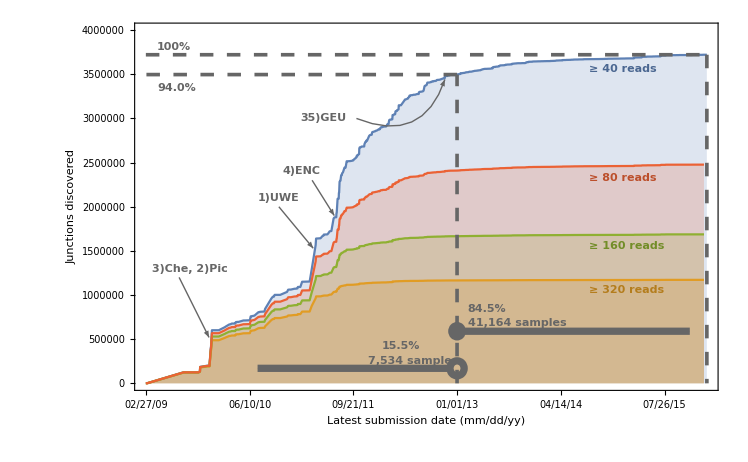

```mathematica
labelColor=Darker[Gray,0.2];leftPos=2000;botPos=140000;fig2=Show[baseJunctionsPlot, Graphics[{labelColor,Arrow[{{150,1.2*10^6},{285,520000}}],arrowLabelForm["3)Che, 2)Pic", {200,1.3*10^6}],Arrow[{{600,2*10^6},{755,1.53*10^6}}],arrowLabelForm["1)UWE       ", {600,2.1*10^6}],Arrow[{{750,2.3*10^6},{850,1.9*10^6}}],Arrow[BezierCurve[{{950,3*10^6},{1249,2.7*10^6},{1349,3.44*10^6}}]],arrowLabelForm["4)ENC", {700,2.4*10^6}], Directive[Thickness[0.0035],Dashing[0.013], labelColor],arrowLabelForm["35)GEU", {800,3*10^6}], Directive[Thickness[0.0035],Dashing[0.013], labelColor],Line[{{twentyThirteen,0},{twentyThirteen,maxAtTwentyThirteen}}],Line[{{twentyThirteen,maxAtTwentyThirteen},{0,maxAtTwentyThirteen}}],Line[{{lastDay,maxAtEnd},{lastDay,0}}],Line[{{0,maxAtEnd},{lastDay,maxAtEnd}}],arrowLabelForm["100%", {50, 3.81*10^6}, {-1,0}],biggerLabelForm[ToString[NumberForm[N[maxAtTwentyThirteen/maxAtEnd*100,3],DigitBlock->3]]<>"%", {50, 3.35*10^6}, {-1,0}],Darker[mathematicaColors[[2]],0.2],arrowLabelForm["≥ 320 reads", {leftPos, 1.055*10^6}, {-1,0}],Darker[mathematicaColors[[3]],0.2],arrowLabelForm["≥ 160 reads", {leftPos, 1.56*10^6}, {-1,0}],Darker[mathematicaColors[[4]],0.2],arrowLabelForm["≥ 80 reads", {leftPos, 2.33*10^6}, {-1,0}],Darker[mathematicaColors[[1]],0.2],arrowLabelForm["≥ 40 reads", {leftPos,  3.56*10^6}, {-1,0}], Dashing[None],Thickness[.007],Darker[Gray, .2],Arrowheads[{0,.05}],smallerLabelForm[ToString[NumberForm[after2013,DigitBlock->3]]<>" samples", {twentyThirteen+50,botPos+540000}, {-1,0}],
biggerLabelForm[ToString[NumberForm[N[after2013/(after2013+before2013)*100,3],DigitBlock->3]]<>"%", {twentyThirteen+45,botPos+700000}, {-1,0}],
smallerLabelForm[ToString[NumberForm[before2013,DigitBlock->3]]<>" samples", {twentyThirteen-400,258000}, {-1,0}],
biggerLabelForm[ToString[NumberForm[N[before2013/(after2013+before2013)*100,3],DigitBlock->3]]<>"%", {twentyThirteen-340,258000+160000}, {-1,0}],Arrow[{{twentyThirteen+18, botPos+450000},{twentyThirteen+1050, botPos+450000}}], Disk[{twentyThirteen, botPos+450000}, {40,105000}],Arrow[{{twentyThirteen-23,170000},{twentyThirteen-900, 170000}}],Circle[{twentyThirteen, 170000}, {32,85000}]}]]
```

```mathematica
Export["dateplot.pdf", fig2]
```

dateplot.pdf

Format of next list is {GENCODE index, date}.

```mathematica
earliestGencodes={#[[2]],#[[1,1,1]]}&/@Select[{Position[#[[Range[5,22]]], 1],#[[4]]}&/@junctionsEvidenceVsDatesGeq20, Length[#[[1]]]>0&];
```

Freeze dates taken from http://www.gencodegenes.org/releases/ .

```mathematica
daysAfterDate [y_]:=DateDifference[DateObject[{2009, 2, 27}],y]
```

```mathematica
gencodeFreezeDates={DateObject[{2009,7}],DateObject[{2009,7}],DateObject[{2010,1}],DateObject[{2010,4}],DateObject[{2010,11}],DateObject[{2010,12}],DateObject[{2011,3}],DateObject[{2011,5}],DateObject[{2011,7}],DateObject[{2011,10}],DateObject[{2011,12}],DateObject[{2012,3}],DateObject[{2012,6}],DateObject[{2012,8}],DateObject[{2012,11}],DateObject[{2013,2}],DateObject[{2013,4}],DateObject[{2013,7}]};
```

```mathematica
gencodeAppearDates={DateObject[{2009,9}],DateObject[{2010,3}],DateObject[{2010,5}],DateObject[{2010,11}],DateObject[{2011,2}],DateObject[{2011,4}],DateObject[{2011,6}],DateObject[{2011,9}],DateObject[{2011,12}],DateObject[{2012,2}],DateObject[{2012,5}],DateObject[{2012,7}],DateObject[{2012,10}],DateObject[{2013,1}],DateObject[{2013,4}],DateObject[{2013,6}],DateObject[{2013,9}],DateObject[{2013,12}]};
```

```mathematica
gencodeFreezeDays=QuantityMagnitude/@daysAfterDate/@gencodeFreezeDates
```

{124,124,308,398,612,642,732,793,854,946,1007,1098,1190,1251,1343,1435,1494,1585}

```mathematica
gencodeAppearDays=QuantityMagnitude/@daysAfterDate/@gencodeAppearDates
```

{186,367,428,612,704,763,824,916,1007,1069,1159,1220,1312,1404,1494,1555,1647,1738}

```mathematica
appearDateFormat={"Month","/","YearShort"};
```

```mathematica
gencodeAppearDateTicks={#,DateString[daysToDate[#],appearDateFormat]}&/@gencodeAppearDays
```

{{186,09/09},{367,03/10},{428,05/10},{612,11/10},{704,02/11},{763,04/11},{824,06/11},{916,09/11},{1007,12/11},{1069,02/12},{1159,05/12},{1220,07/12},{1312,10/12},{1404,01/13},{1494,04/13},{1555,06/13},{1647,09/13},{1738,12/13}}

```mathematica
discoveryDaysToGencodeDays={#[[1]],gencodeAppearDays[[#[[2]]]]}&/@earliestGencodes;
```

```mathematica
toAcc=SortBy[Tally[#[[1]]&/@earliestGencodes], First];accumulatedAnnotated=Transpose[{toAcc[[All,1]],Accumulate[toAcc[[All,2]]]}];
```

```mathematica
baseImageSize
```

{748.8,530.4}

```mathematica
toBoxWhisker=Table[#[[1]]&/@Select[discoveryDaysToGencodeDays, #[[2]]==i&], {i, gencodeAppearDays}];
```

```mathematica
toBar=Length/@toBoxWhisker
```

{251810,1145,10593,5478,7188,9319,3455,3119,2579,4879,2088,3196,4599,3265,553,515,542,667}

```mathematica
chartColors={-Graphics-,Lighter[Gray, .5]}
```

{RGBColor[0.982864, 0.7431472, 0.3262672],RGBColor[0.75, 0.75, 0.75]}

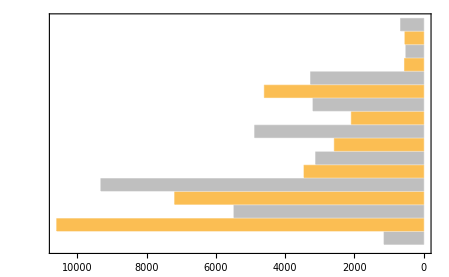

```mathematica
insetBars=BarChart[toBar[[Range[2,18]]], ImageSize->baseImageSize*0.6, Frame->True,FrameTicks->{{None, Automatic}, {Automatic, None}},ChartLabels->{Style[#,13]&/@gencodeAppearDateTicks[[Range[2,18],2]]},  BaseStyle->{FontFamily->"Arial", FontSize->14}, ChartStyle->{chartColors[[2]], chartColors[[1]]},PlotRangePadding->{{500,0},{0.3,0.5}}, BarOrigin->Right]
```

```mathematica
toBar=Length/@toBoxWhisker
```

{251810,1145,10593,5478,7188,9319,3455,3119,2579,4879,2088,3196,4599,3265,553,515,542,667}

```mathematica
toBar[[1]]/Total[toBar]//N
```

0.799422

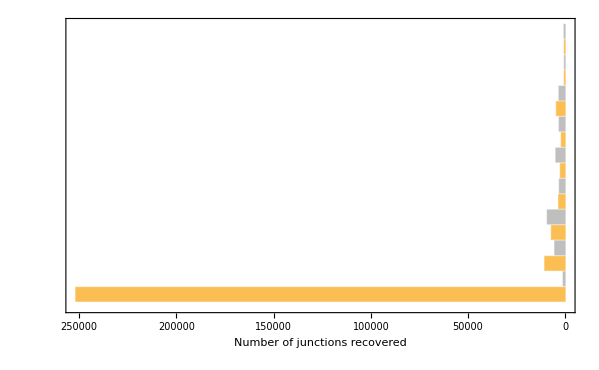

```mathematica
padding={{10,70},{50,0}};barsWithInset=BarChart[toBar, ImageSize->baseImageSize*.8, Frame->True,FrameTicks->{{None, Automatic},{ Automatic, None}},PlotRangePadding->{{10000,0},{.3,.5}},ChartLabels->{StringJoin["  ", #]&/@gencodeAppearDateTicks[[All,2]]},  BaseStyle->{FontFamily->"Arial", FontSize->14},FrameLabel->{{None, Style["Date of first appearance in GENCODE (mm/yy)", 13]}, {Style["Number of junctions recovered", 22],None}}, ChartStyle->chartColors, ImagePadding->padding,BarOrigin->Right,Epilog->Inset[insetBars, {-135000,10}, Automatic, 210000]]
```

```mathematica
magFlipped=Import["magflipped.png"]
```

-Graphics-

```mathematica
origDateTicks=({#,DateString[daysToDate[#], dateFormat]}&/@Range[0, 2070, 329.3])
```

{{0.,02/27/09},{329.3,01/22/10},{658.6,12/17/10},{987.9,11/11/11},{1317.2,10/06/12},{1646.5,08/31/13},{1975.8,07/26/14}}

```mathematica
newDateTicks={{0.,"    02/27/09"},{329.3,"01/22/10"},{658.6,"12/17/10"},{987.9000000000001,"11/11/11"},{1317.2,"10/06/12"},{1646.5,"08/31/13"},{1975.8000000000002,"07/26/14"}}
```

{{0.,    02/27/09},{329.3,01/22/10},{658.6,12/17/10},{987.9,11/11/11},{1317.2,10/06/12},{1646.5,08/31/13},{1975.8,07/26/14}}

```mathematica
sampleCountsInFirstGencode=#[[2]]&/@Select[junctionsEvidenceVsDatesGeq20, #[[5]]==1&];sampleCountsInOtherGencodes=#[[2]]&/@Select[junctionsEvidenceVsDatesGeq20, #[[5]]==0&&Length[Position[#[[Range[5,22]]], 1]]≠0&];
```

```mathematica
anotherLabelForm [x_,y___]:= Text[Style[x, FontFamily->"Arial", FontSize->14, Bold,TextAlignment->Left], y]
```

```mathematica
daysToDate[329]
```

Fri 22 Jan 2010

```mathematica
proportionOfTotalAt329=ToString[NumberForm[N[Select[accumulatedJunctionsGeq[20],#[[1]]≤329&][[-1]][[2]]/accumulatedJunctionsGeq[20][[-1]][[2]]*100,3],DigitBlock->3]]
```

20.3

```mathematica
totBound=Select[accumulatedJunctionsGeq[20],#[[1]]≤329&][[-1]][[2]]
```

651644

```mathematica
proportionOfAnnotatedAt329=ToString[NumberForm[N[Select[accumulatedAnnotated,#[[1]]≤329&][[-1]][[2]]/accumulatedAnnotated[[-1]][[2]]*100,3],DigitBlock->3]]
```

74.2

```mathematica
annBound=Select[accumulatedAnnotated,#[[1]]≤329&][[-1]][[2]]
```

233834

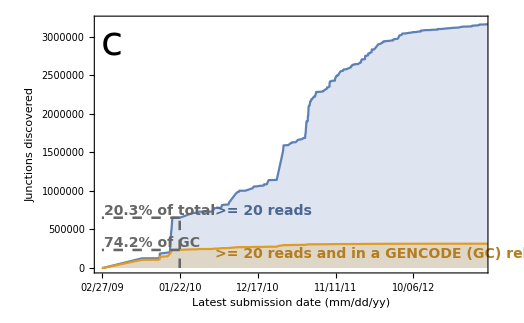

```mathematica
annJunctionsPlot=ListPlot[{accumulatedJunctionsGeq[20],accumulatedAnnotated}, Joined->True,Filling->Axis, Frame->True, FrameTicks->{{Automatic,None},{origDateTicks, None}},BaseStyle->{FontFamily->"Arial",FontSize->14}, FrameLabel->{Style["Latest submission date (mm/dd/yy)", 22, TextAlignment->Left], Style["Junctions discovered", 22]}, ImageSize->baseImageSize*0.7, PlotRange->{{Automatic,1600}, {0, 3.2*10^6}}];annJunctionsComplete=Show[annJunctionsPlot,Graphics[{Darker[mathematicaColors[[1]], 0.2], anotherLabelForm[">= 20 reads", {480,735000}, {-1,0}],Darker[mathematicaColors[[2]], 0.2], anotherLabelForm[">= 20 reads and in a GENCODE (GC) release", {480,187000}, {-1,0}], Directive[Thickness[0.0035],Dashing[0.013], labelColor], Line[{{329,0},{329,totBound}}], Line[{{329,annBound},{0,annBound}}],anotherLabelForm[ToString[proportionOfAnnotatedAt329]<>"% of GC", {8, annBound+90000}, {-1,0}],Line[{{329,totBound},{0,totBound}}],anotherLabelForm[ToString[proportionOfTotalAt329]<>"% of total", {8, totBound+90000}, {-1,0}]}],Graphics[{Black,Text[Style["c", FontFamily->"Arial", FontSize->40], {40,2.9*10^6}]}]]
```

```mathematica
altLabelForm [x_,y___]:= Text[Style[x, FontFamily->"Arial", FontSize->Scaled[.02],Bold,TextAlignment->Left], y]
```

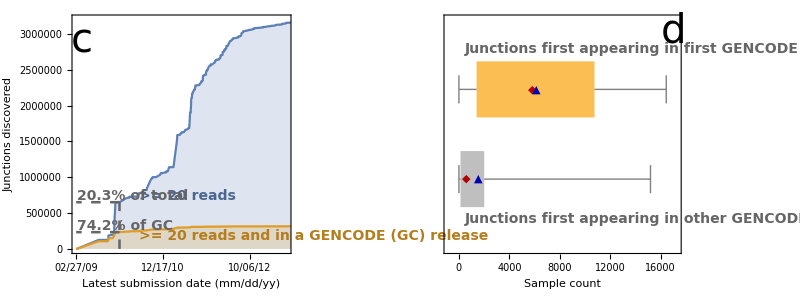
-Graphics-
-Graphics-

```mathematica
sampleBoxPlot=Show[BoxWhiskerChart[{sampleCountsInOtherGencodes,sampleCountsInFirstGencode},{{"MeanMarker","▲", Darker[Blue, 0.3]},{"MedianMarker","◆", Darker[Red, 0.3]}},ImageSize->baseImageSize*.613,ChartStyle->{chartColors[[2]],chartColors[[1]]},BarOrigin->Left,BarSpacing->Medium,Frame->True, FrameLabel->{Style["Sample count", 22], None},BaseStyle->{FontFamily->"Arial", FontSize->14}], Graphics[{Darker[Gray,0.2], anotherLabelForm["Junctions first appearing in first GENCODE release", {500, 2.45}, {-1,0}], anotherLabelForm["Junctions first appearing in other GENCODE releases", {500, .55}, {-1,0}]}],Graphics[{Black,Text[Style["d", FontFamily->"Arial", FontSize->40], {17000,2.65}]}]];leftOff=-145000;upOff=90000;suppevleft=Show[barsWithInset, Graphics[{Black,Text[Style["a", FontFamily->"Arial", FontSize->40], {-250000,17.5}],Gray,Arrow[BezierCurve[{{-16000,16.6},{-30000,18.8},{-45000,17.6}}]],Thickness[.003],Line[{{-13000,18.3},{-13000,1.8}}]}], Graphics[{Opacity[0.5],Inset[magFlipped,{-30000,17.4},{0,0},12000]}], ImageSize->baseImageSize*0.7];otherpadding={{0,10},{50,0}};suppevright=Show[BoxWhiskerChart[toBoxWhisker,{{"MeanMarker","▲", Darker[Blue, 0.3]},{"MedianMarker","◆", Darker[Red, 0.3]}},ImageSize->baseImageSize*.613,ChartStyle->chartColors,BarOrigin->Left,BarSpacing->Medium,Frame->True, PlotRange->{Automatic, Automatic},PlotRangePadding->{{0.1,0.9},{0.3,0.5}},ImagePadding->otherpadding,FrameTicks->{{None, None},{newDateTicks, None}}, BaseStyle->{FontFamily->"Arial", FontSize->14},FrameLabel->{Style["Junction discovery date (mm/dd/yy)",22], None}],Graphics[{Black,Text[Style["b", FontFamily->"Arial", FontSize->40], {1985,17.8}]}]];suppevall=Grid[{{Grid[{{suppevleft,suppevright}}]},{Grid[{{annJunctionsComplete,sampleBoxPlot}}]}}]
```

```mathematica
Export["ev.pdf",suppevall]
```

ev.pdf

Assess strength of correlation between discovery date and Gencode date. Even rank correlation is small.

```mathematica
SpearmanRankTest[discoveryDaysToGencodeDays[[All,1]],discoveryDaysToGencodeDays[[All,2]], "TestDataTable"]//N
```

| Statistic | P-Value
Spearman Rank | 0.356502 | 2.26782581×10^-9300

Exclude 2/28/09; relationship between it and the rest may be the dominant effect.

```mathematica
daysToDate[186]
```

Tue 1 Sep 2009

```mathematica
discoveryDaysToGencodeDaysNoFirst=Select[discoveryDaysToGencodeDays, #[[2]]≠186&];
```

```mathematica
SpearmanRankTest[discoveryDaysToGencodeDaysNoFirst[[All,1]],discoveryDaysToGencodeDaysNoFirst[[All,2]], "TestDataTable"]//N
```

| Statistic | P-Value
Spearman Rank | -0.0148139 | 0.00019633

... and this is true. Now let’s load and plot PCs.

```mathematica
pcData=Import["!cat pcs_unannotated_with_pd.tsv | tr -s '[:blank:]' '\t'", "TSV"];
```

```mathematica
pcHeader=pcData[[1]]
```

{PC1,PC2,PC3,PC4,PC5,brain,lcl,blood,seqc_abrf,geuvadis,mixture}

```mathematica
pcData=pcData[[Range[2,Length[pcData]]]];
```

```mathematica
brain=Select[pcData, #[[7]]==1&];lcl=Select[pcData,#[[8]]==1&];blood=Select[pcData,#[[9]]==1&];oneToZero=Select[pcData,#[[-1]]=="1:0"&];threeToOne=Select[pcData,#[[-1]]=="3:1"&];oneToThree=Select[pcData,#[[-1]]=="1:3"&];zeroToOne=Select[pcData,#[[-1]]=="0:1"&];others=Select[pcData, #[[7]]≠1 &&#[[8]]≠1&&#[[9]]≠1&&#[[-1]]=="NA"&];geuvadis=Select[pcData,#[[-2]]==1&];abrf=Select[pcData,#[[-3]]==2&];seqc=Select[pcData,#[[-3]]==1&];
```

```mathematica
mathematicaColors
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

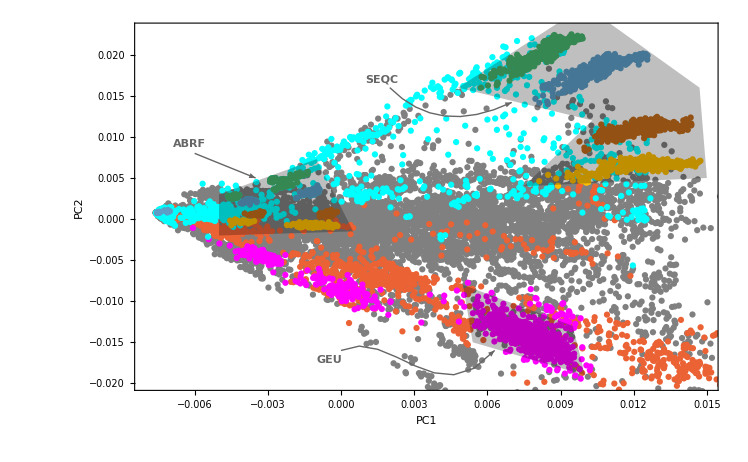

```mathematica
arrowLabelForm [x_,y___]:= Text[Style[x, FontFamily->"Arial", FontSize->Scaled[.03],Bold,TextAlignment->Left], y];labelColor=Darker[Gray,0.2];pcaPlot=Show[ListPlot[Transpose[{#[[All,2]],#[[All,3]]}]&/@{others,blood, lcl,brain,oneToZero, oneToThree,threeToOne, zeroToOne}, Frame->True, ImageSize->baseImageSize, PlotRange->{{-.008,.015},{-.02,.023}},Axes->None,FrameLabel->{Style["PC1", 22, TextAlignment->Left], Style["PC2", 22]},BaseStyle->{FontFamily->"Arial",FontSize->14} , PlotStyle->{{PointSize[.006], Gray},{PointSize[.006], mathematicaColors[[4]]},{PointSize[.006],Magenta},{PointSize[.006], Cyan},{PointSize[.006], mathematicaColors[[15]]},PointSize[.006],PointSize[.006],PointSize[.006]}], Graphics[{Opacity[0.25],Polygon[{{-.005,-.002}, {-.005,.003},{-.001,.0073},{0.0005,-0.0015}}],Polygon[{{.0075,.004},{.0103,.012}, {.0048,.016},{.01,.026},{.0147,.016},{0.015
,0.005}}], Polygon[{{.0054, -.015}, {.005,-.008},{.0095,-.013},{.01,-.019}}],Opacity[1],labelColor,Arrow[{{-.006,.008},{-.0035,.005}}], arrowLabelForm["ABRF", {-.0069,.0092}, {-1,0}],Arrow[BezierCurve[{{.002,.016},{.004,.01},{.007,.0142}}]],arrowLabelForm["SEQC", {.001,.017}, {-1,0}],Arrow[BezierCurve[{{0,-.016},{.002,-.013},{.004,-.024},{.0063,-.016}}]],arrowLabelForm["GEU", {-.001,-.0172}, {-1,0}]}]]
```

```mathematica
Export["pca.pdf",pcaPlot]
```

pca.pdf